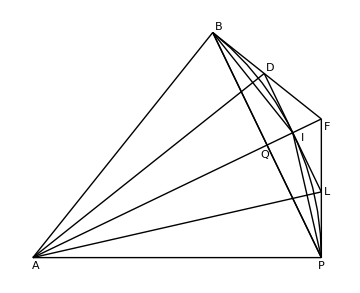

```mathematica
SetOptions[Graphics,BaseStyle->{FontFamily->"Times",FontSize->30,FontSlant-> Plain}];
Show[
Graphics[{
Circle[{0,0},1,{0,2*Pi/7}],
Line[{{0,0},{1,0}}],
Line[{{0,0},{1,Tan[(Pi)/7]}}],
Line[{{1,0},{1, Tan[(Pi)/7]}}],
Line[{{0,0},{Cos[2*Pi/7],Sin[2*Pi/7]}}],
Line[{{1,0},{Cos[2*Pi/7],Sin[2*Pi/7]}}],
Line[{{1,0},{Cos[2*Pi/7],Sin[2*Pi/7]}}],
Line[{{1, Tan[(Pi)/7]},{Cos[2*Pi/7],Sin[2*Pi/7]}}],
Line[{{1,0},{Cos[Pi/7],Sin[Pi/7]}}],
Line[{{Cos[2*Pi/7],Sin[2*Pi/7]},{Cos[Pi/7],Sin[Pi/7]}}],
Line[{{1,-Cot[Pi/7]*(1-Cos[Pi/7])+Sin[Pi/7]},{(-Cos[(3 π)/14]+Cos[π/7] Cot[π/7]+Sin[π/7]-Sin[(3 π)/14] Tan[(3 π)/14])/(Cot[π/7]-Tan[(3 π)/14]),(Cos[(3 π)/14] Cot[π/7]-1/16 Csc[π/14] Csc[π/7]^2+(-Sin[π/7]+Cot[π/7] Sin[(3 π)/14]) Tan[(3 π)/14])/(Cot[π/7]-Tan[(3 π)/14])}}],
Line[{{0,0},{(-Cos[(3 π)/14]+Cos[π/7] Cot[π/7]+Sin[π/7]-Sin[(3 π)/14] Tan[(3 π)/14])/(Cot[π/7]-Tan[(3 π)/14]),(Cos[(3 π)/14] Cot[π/7]-1/16 Csc[π/14] Csc[π/7]^2+(-Sin[π/7]+Cot[π/7] Sin[(3 π)/14]) Tan[(3 π)/14])/(Cot[π/7]-Tan[(3 π)/14])}}],
Line[{{0,0},{1,-Cot[Pi/7]*(1-Cos[Pi/7])+Sin[Pi/7]}}],
Text["A",{0.01,-.03},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant-> Plain}],
Text["P",{1,-.03},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant-> Plain}],
Text["F",{1.02,Sin[Pi/7]+.02},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant-> Plain}],
Text["B",{Cos[2*Pi/7]+.02,Sin[2*Pi/7]+.02},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant-> Plain}],
Text["I",{Cos[Pi/7]+.035,Sin[Pi/7]-.02},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant-> Plain}],
Text["Q",{0.803,.357},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant-> Plain}],
Text["D",{(-Cos[(3 π)/14]+Cos[π/7] Cot[π/7]+Sin[π/7]-Sin[(3 π)/14] Tan[(3 π)/14])/(Cot[π/7]-Tan[(3 π)/14])+.02,(Cos[(3 π)/14] Cot[π/7]-1/16 Csc[π/14] Csc[π/7]^2+(-Sin[π/7]+Cot[π/7] Sin[(3 π)/14]) Tan[(3 π)/14])/(Cot[π/7]-Tan[(3 π)/14])+.02},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant-> Plain}],
Text["L",{1.02,-Cot[Pi/7]*(1-Cos[Pi/7])+Sin[Pi/7]},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant-> Plain}]
}
],
ImageSize->Medium]
```

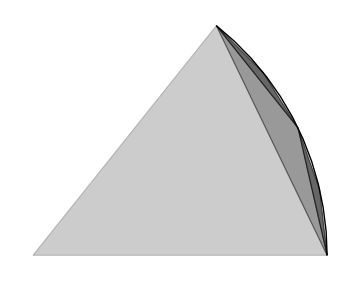

```mathematica
Show[
Graphics[{
Circle[{0,0},1,{0,2*Pi/7}],
{
Black,
EdgeForm[Thin],
Opacity[0.6],
Polygon[{{Cos[Pi/7],Sin[Pi/7]},{Cos[3*Pi/14],Sin[3*Pi/14]},{Cos[2*Pi/7],Sin[2*Pi/7]}}]
},
{
Black,
EdgeForm[Thin],
Opacity[0.6],
Polygon[{{1,0},{Cos[Pi/7],Sin[Pi/7]},{Cos[Pi/14],Sin[Pi/14]}}]
},
{
Black,
EdgeForm[Thin],
Opacity[0.4],
Polygon[{{1,0},{Cos[2*Pi/7],Sin[2*Pi/7]},{Cos[Pi/7],Sin[Pi/7]}}]
},
{
Black,
EdgeForm[Thin],
Opacity[0.2],
Polygon[{{0,0},{1,0},{Cos[2*Pi/7],Sin[2*Pi/7]}}]
}
}],
ImageSize->Medium
]
```

```mathematica
Export["vera_inscr.pdf",%70,"PDF"]
```

vera_inscr.pdf

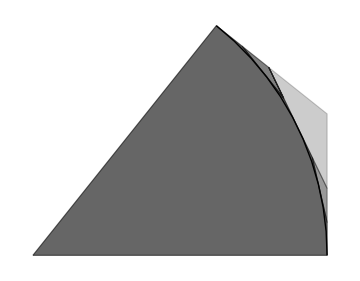

```mathematica
Show[
Graphics[{
Circle[{0,0},1,{0,2*Pi/7}],
{
Black,
EdgeForm[Thin],
Opacity[0.5],
Polygon[{
{Sqrt[(1+(Tan[Pi/14])^2)/(1+(Tan[3*Pi/14])^2)],Tan[3*Pi/14]*Sqrt[(1+(Tan[Pi/14])^2)/(1+(Tan[3*Pi/14])^2)]},
{Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[5*Pi/28])^2)],Tan[5*Pi/28]*Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[5*Pi/28])^2)]},
{Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[7*Pi/28])^2)],Tan[7*Pi/28]*Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[7*Pi/28])^2)]}
}]
},
{
Black,
EdgeForm[Thin],
Opacity[0.4],
Polygon[{
{Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[3*Pi/28])^2)],Tan[3*Pi/28]*Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[3*Pi/28])^2)]},
{1,Tan[(Pi)/14]},
{1,Tan[(Pi)/28]}
}]
},
{
Black,
EdgeForm[Thin],
Opacity[0.2],
Polygon[{
{Sqrt[(1+(Tan[Pi/14])^2)/(1+(Tan[3*Pi/14])^2)],Tan[3*Pi/14]*Sqrt[(1+(Tan[Pi/14])^2)/(1+(Tan[3*Pi/14])^2)]},
{1,Tan[(Pi)/7]},
{1,Tan[(Pi)/14]}
}]
},
{
Black,
EdgeForm[Thin],
Opacity[0.6],
Polygon[{
{0,0},
{1,0},
{1,Tan[(Pi)/28]},
{Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[3*Pi/28])^2)],Tan[3*Pi/28]*Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[3*Pi/28])^2)]},
{Sqrt[(1+(Tan[Pi/14])^2)/(1+(Tan[3*Pi/14])^2)],Tan[3*Pi/14]*Sqrt[(1+(Tan[Pi/14])^2)/(1+(Tan[3*Pi/14])^2)]},
{Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[5*Pi/28])^2)],Tan[5*Pi/28]*Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[5*Pi/28])^2)]},
{Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[7*Pi/28])^2)],Tan[7*Pi/28]*Sqrt[(1+(Tan[Pi/28])^2)/(1+(Tan[7*Pi/28])^2)]},
{Cos[2*Pi/7],Sin[2*Pi/7]}
}]
},
}],

ImageSize->Medium
]
```

```mathematica
Export["vera_circumscr.pdf",%68,"PDF"]
```

vera_circumscr.pdf

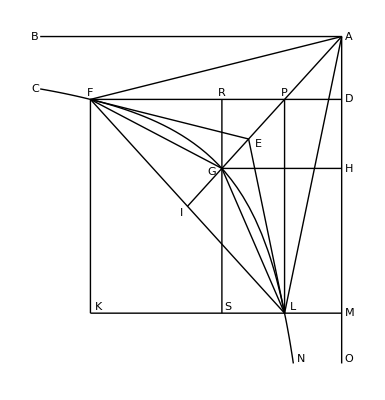

```mathematica
Show[{
Graphics[{
{
Line[{{0,0},{-12/5,0}}],
Line[{{0,0},{0,-13/5}}],
Line[{{0,0},{-2,-1/2}}],
Line[{{0,0},{-5/11,-11/5}}],
Line[{{0,0},{-27/22,-27/20}}],
Line[{{-2,-1/2},{0,-1/2}}],
Line[{{-2,-1/2},{-20/27,-22/27}}],
Line[{{-2,-1/2},{-Sqrt[10/11],-Sqrt[11/10]}}],
Line[{{-2,-1/2},{-5/11,-11/5}}],
Line[{{-2,-1/2},{-2,-11/5}}],
Line[{{-Sqrt[10/11],-1/2},{-Sqrt[10/11],-11/5}}],
Line[{{-Sqrt[10/11],-Sqrt[11/10]},{0,-Sqrt[11/10]}}],
Line[{{-5/11,-11/5},{-5/11,-1/2}}],
Line[{{-5/11,-11/5},{-20/27,-22/27}}],
Line[{{-5/11,-11/5},{-Sqrt[10/11],-Sqrt[11/10]}}],
Line[{{0,-11/5},{-2,-11/5}}]
},
{
Text["A",{3/50,0},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["B",{-122/50,0},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["C",{-122/50,-5/12},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["D",{3/50,-1/2},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["E",{-18/27,-23/27},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["F",{-2,-9/20},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["G",{-166/160,-172/160},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["H",{3/50,-21/20},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["I",{-14/11,-14/10},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["K",{-155/80,-43/20},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["L",{-5/13,-43/20},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["M",{13/200,-11/5},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["N",{-17/52,-205/80},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["O",{3/50,-205/80},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["P",{-5/11,-9/20},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["R",{-Sqrt[10/11],-9/20},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["S",{-10/11,-43/20},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}]
}
}],
Plot[{1/x},{x,-12/5,0},PlotRange->{0,-13/5},AspectRatio->13/12,Axes->False,PlotStyle->Black]
}]
```

```mathematica
Export["vera_hyp_i.pdf",%151,"PDF"]
```

vera_hyp_i.pdf

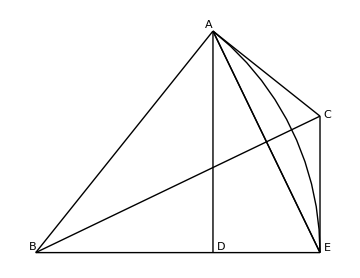

```mathematica
Show[
Graphics[{
Circle[{0,0},1,{0,2*Pi/7}],
Line[{{0,0},{1,0}}],
Line[{{0,0},{1,Tan[(Pi)/7]}}],
Line[{{1,0},{1,Tan[(Pi)/7]}}],
Line[{{0,0},{Cos[2*Pi/7],Sin[2*Pi/7]}}],
Line[{{1,0},{Cos[2*Pi/7],Sin[2*Pi/7]}}],
Line[{{1,0},{Cos[2*Pi/7],Sin[2*Pi/7]}}],
Line[{{1,Tan[(Pi)/7]},{Cos[2*Pi/7],Sin[2*Pi/7]}}],
Line[{{Cos[2*Pi/7],Sin[2*Pi/7]},{Cos[2*Pi/7],0}}],
Text["B",{-0.01,.02},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["E",{1.025,0.015},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["C",{1.025,Sin[Pi/7]+.05},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["A",{Cos[2*Pi/7]-.015,Sin[2*Pi/7]+.02},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["D",{Cos[2*Pi/7]+0.027,0.02},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}]
}],
ImageSize->Medium
]
```

```mathematica
Export["vera_ii.pdf",%34,"PDF"]
```

vera_ii.pdf

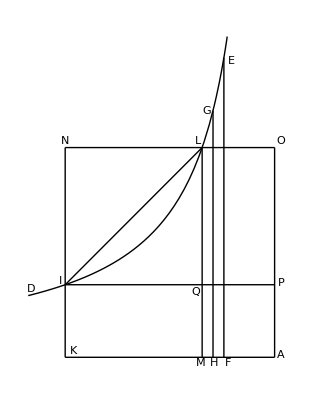

```mathematica
Show[
Graphics[{
{
Line[{{0,0},{-17/10,0}}],
Line[{{0,0},{0,17/10}}],
Line[{{-17/10,17/10},{-17/10,0}}],
Line[{{-17/10,17/10},{0,17/10}}],
Line[{{-10/17,0},{-10/17,17/10}}],
Line[{{0,10/17},{-17/10,10/17}}],
Line[{{-10/17,17/10},{-17/10,10/17}}],
Line[{{-17/34,0},{-17/34,34/17}}],
Line[{{-14/34,0},{-14/34,34/14}}]
},
{
Text["A",{0.05,0.02},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["D",{-1.98,.55},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["E",{-0.35,2.4},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["F",{-0.38,-0.05},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["G",{-0.55,2.0},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["H",{-0.49,-0.05},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["I",{-1.74,0.62},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["K",{-1.63,0.05},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["L",{-0.62,1.75},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["M",{-0.6,-0.05},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["N",{-1.7,1.75},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["O",{0.05,1.75},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["P",{0.05,0.6},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["Q",{-0.64,0.53},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}]
}
}],
Plot[-1/x,{x,-10/5,0},PlotRange->{0,13/5},AspectRatio->1,PlotStyle->Black]
]
```

```mathematica
Export["vera_hyp_ii.pdf",%154,"PDF"]
```

vera_hyp_ii.pdf

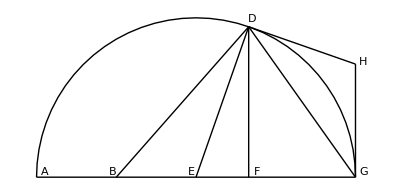

```mathematica
Show[
Graphics[{
Circle[{0,0},1,{0,Pi}],
{
Line[{{-1,0},{1,0}}],
Line[{{0,0},{Cos[11*Pi/28],Sin[11*Pi/28]}}],
Line [{{-1/2,0},{Cos[11*Pi/28],Sin[11*Pi/28]}}],
Line[{{Cos[11*Pi/28],0},{Cos[11*Pi/28],Sin[11*Pi/28]}}],
Line[{{1,0},{Cos[11*Pi/28],Sin[11*Pi/28]}}],
Line[{{1,0},{1,(-Cot[(11*Pi)/28])*(1-Cos[11*Pi/28])+Sin[11*Pi/28]}}],
Line[{{Cos[11*Pi/28],Sin[11*Pi/28]},{1,(-Cot[(11*Pi)/28])*(1-Cos[11*Pi/28])+Sin[11*Pi/28]}}]
},
{
Text["A",{-.95,0.035},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["B",{-.52,0.035},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["D",{0.35,0.99},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["E",{-.03,0.035},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["F",{0.38,0.035},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["G",{1.05,0.035},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}],
Text["H",{1.05,0.72},BaseStyle->{FontFamily->"Times",FontSize->16,FontSlant->Plain}]
}
}]
]
```

```mathematica
Export["vera_semicirc.pdf",%37,"PDF"]
```

vera_semicirc.pdf